```mathematica
f = Function[t,Piecewise[{{Exp[1/t], t ≠ 0}, {0, t==0}}]]
```

Function[t,Piecewise[{{Exp[1/t], t≠0}, {0, t==0}}]]

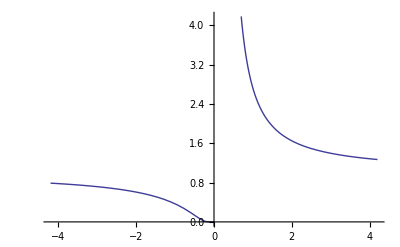

```mathematica
Plot[Function[t,Piecewise[{{Exp[1/t],t≠0},{0,t==0}}]][x],{x,-4.2,4.2}]
```

```mathematica
g = Function[t,f[t]/(f[t] + f[1-t])]
```

Function[t,f[t]/(f[t]+f[1-t])]

```mathematica
h = Function[t,g[t+2] g[2-t]]
```

Function[t,g[t+2] g[2-t]]

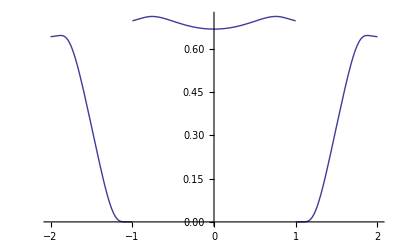

```mathematica
Plot[Function[t,g[t+2] g[2-t]][x],{x,-2,2}]
```